```mathematica
ImportCsv[name_] := Import["~/workspace/PBLL/LieDetector/Analysis/" <> name <> ".csv","Dataset","HeaderLines"->1]
```

```mathematica
MeansFromCenter[name_, selectColumn_:"", selectValue_:""] :=
Block[{columns, dataset, allValues, center, grouped, groupedColumns, groupedValues, allDistances, allMeans},
columns = {"Combine Gaze X","Combine Gaze Y"};
dataset=If[StringLength[selectColumn]>0,Select[ImportCsv[name], #[selectColumn] == selectValue&], ImportCsv[name]];
allValues=Values[dataset[All,columns]];
center={Mean[allValues[All,1]],Mean[allValues[All,2]]};

grouped=dataset[GroupBy["Index"]];
groupedColumns = Table[grouped[[x]][All, columns], {x, 1, Length[grouped], 1}];
groupedValues = (Normal[Values[#]])& /@ groupedColumns;
allDistances=((ArcLength[Line[{#,center}]])& /@ #)&/@groupedValues;
allMeans = (Mean[#])& /@ allDistances;
allMeans
]
```

```mathematica
TimeToAnswer[name_] := 
Block[{dataset, grouped, times},
dataset = ImportCsv[name];
grouped = dataset[GroupBy["Index"]];
times = Table[grouped[[x]][All, "Total Time"], {x, 1, Length[grouped], 1}];
(Last[#] - First[#])& /@ times
]
```

```mathematica
IndividualClassifierData[dataset_, truth_:""]:=
Block[{eyeColumns, eyeValues, center, distances, meanDistance, timeValues, timeToAnswer},
eyeColumns = {"Combine Gaze X","Combine Gaze Y"};
eyeValues =  Values[dataset[All,eyeColumns]];
center = {Mean[eyeValues[All, 1]], Mean[eyeValues[All, 2]]};
distances  = (ArcLength[Line[{#,center}]])& /@ eyeValues;
meanDistance = Mean[distances];

timeValues = Values[dataset[All, {"Total Time"}]];
timeToAnswer = Last[timeValues][[1]] - First[timeValues][[1]];
If[StringLength[truth] > 0,{meanDistance, timeToAnswer} -> truth, {meanDistance, timeToAnswer}]
]
```

```mathematica
ClassifierAssociation[name_]:=
Block[{dataset, grouped, center},
dataset = ImportCsv[name];
grouped = dataset[GroupBy["Index"]];
Table[IndividualClassifierData[grouped[x], If[StringContainsQ[name, "mixed"], If[grouped[x][1, "Truth"] == "TRUE", "Truth", "Lie"], If[StringContainsQ[name, "truth"], "Truth", "Lie"]]], {x, 1, Length[grouped], 1}]
]
```

```mathematica
ClassifierData[name_]:=
Block[{dataset, grouped, center},
dataset = ImportCsv[name];
grouped = dataset[GroupBy["Index"]];
Table[IndividualClassifierData[grouped[x]], {x, 1, Length[grouped], 1}]
]
```

```mathematica
ImportCsv["mixed"][GroupBy["Index"]][[1]][1, "Truth"]
```

TRUE

```mathematica
IndividualClassifierData[ImportCsv["truth"][GroupBy["Index"]][[1]], "Truth"]
```

0.0250974

```mathematica
classifierData = Join[ClassifierAssociation["truth"], ClassifierAssociation["lies"]]
```

{{0.0250974,1.98816}→Truth,{0.0107385,1.97671}→Truth,{0.0183827,1.97591}→Truth,{0.00959995,1.97571}→Truth,{0.0170957,1.97782}→Truth,{0.005522,1.97692}→Truth,{0.018686,1.97487}→Truth,{0.0169584,1.97579}→Truth,{0.00541573,1.98778}→Truth,{0.00472945,1.97866}→Truth,{0.0151275,1.97799}→Truth,{0.00945566,1.97722}→Truth,{0.00991411,1.97871}→Truth,{0.0141715,1.97662}→Truth,{0.00745786,1.97707}→Truth,{0.034847,2.64233}→Lie,{0.00465258,1.97662}→Lie,{0.0148581,1.97676}→Lie,{0.0195845,1.97533}→Lie,{0.0136559,1.98353}→Lie,{0.0116466,1.97754}→Lie,{0.0145938,1.97799}→Lie,{0.019142,1.966}→Lie,{0.0129175,1.99948}→Lie,{0.0300523,1.9778}→Lie,{0.0113025,1.97805}→Lie,{0.0144082,1.97641}→Lie,{0.019838,1.97568}→Lie,{0.0204582,1.99762}→Lie,{0.0176273,1.99787}→Lie}

```mathematica
c=Classify[classifierData,Method->"LogisticRegression"]
```

ClassifierFunction[…]

```mathematica
(c[#])&/@ClassifierData["lies3"]
```

{Lie,Truth,Truth,Lie,Lie,Truth,Truth,Truth,Lie,Lie,Truth,Truth,Lie,Truth,Truth}

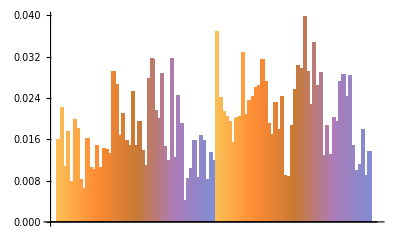

```mathematica
BarChart[{Join[MeansFromCenter["truth"], MeansFromCenter["truth2"],MeansFromCenter["truth3"], MeansFromCenter["mixed", "Truth", "TRUE"]], Join[MeansFromCenter["lies"], MeansFromCenter["lies2"],MeansFromCenter["lies3"], MeansFromCenter["mixed", "Truth", "FALSE"]]}]
```

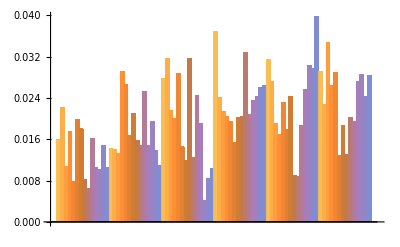

```mathematica
BarChart[{IndividualMeansFromCenter["truth"], IndividualMeansFromCenter["truth2"], IndividualMeansFromCenter["truth3"], IndividualMeansFromCenter["lies"], IndividualMeansFromCenter["lies2"], IndividualMeansFromCenter["lies3"]}]
```

```mathematica
IndividualMeansFromCenter["truth3"]
```

truth3

```mathematica
Mean[Join[IndividualMeansFromCenter["lies"], IndividualMeansFromCenter["lies2"], IndividualMeansFromCenter["lies3"]]]
```

0.0235469

```mathematica
Mean[IndividualMeansFromCenter["mixed"]]
```

0.0127355

```mathematica
Pupils[name_] :=
Block[{columns, dataset, allValues, center, grouped, groupedColumns, groupedValues, allMeans},
columns = {"Left Pupil Diameter", "Right Pupil Diameter"};
dataset=Select[ImportCsv[name], (#["Color"] == "Red")&];

grouped=dataset[GroupBy["Index"]];
groupedColumns = Table[grouped[[x]][All, columns], {x, 1, Length[grouped], 1}];
groupedValues = (Normal[Values[#]])& /@ groupedColumns;
allMeans = (Mean[Mean[{#[[1]], #[[2]]}]])& /@ groupedValues;
allMeans
]
```

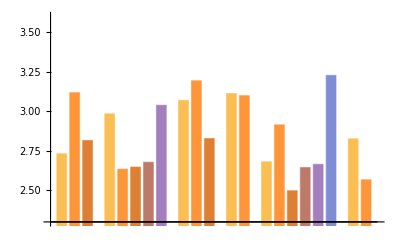

```mathematica
BarChart[{Pupils["truth"], Pupils["truth2"], Pupils["truth3"], Pupils["lies"], Pupils["lies2"], Pupils["lies3"]}, PlotRange->{{2.3,3.6}}]
```

```mathematica
Mean[Join[Pupils["truth"], Pupils["truth2"], Pupils["truth3"]]]
```

2.88514

```mathematica
Mean[Join[Pupils["lies"], Pupils["lies2"], Pupils["lies3"]]]
```

```mathematica
2.8233147
```

```mathematica
colors = (If[# == "FALSE",Red,Blue])& /@Normal[Values[((#[[1]])&/@ImportCsv["mixed"][GroupBy["Index"]])[All, "Truth"]]]
```

{RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, 0, 1]}

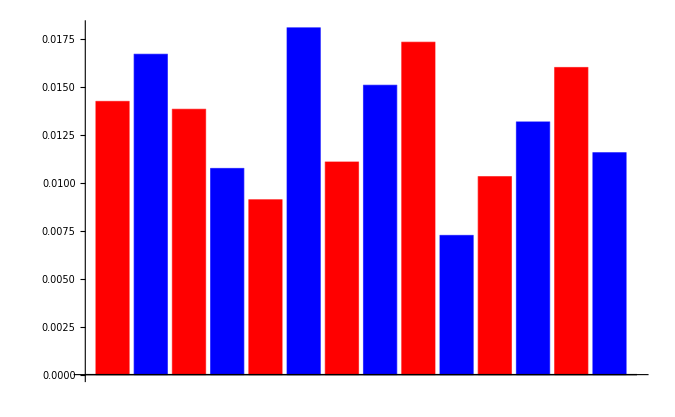

```mathematica
BarChart[IndividualMeansFromCenter["mixed"], ChartStyle-> colors]
```

```mathematica
TimeToAnswer[name_] := 
Block[{dataset, grouped, times},
dataset = ImportCsv[name];
grouped = dataset[GroupBy["Index"]];
times = Table[grouped[[x]][All, "Total Time"], {x, 1, Length[grouped], 1}];
(Last[#] - First[#])& /@ times
]
```

```mathematica
baselineTime = Mean[TimeToAnswer["truth3"]]
```

1.38023

```mathematica
baselineEye = Mean[IndividualMeansFromCenter["truth3"]]
```

0.0190438

```mathematica
EyeDiffFromBaseline[names_, baseline_]:=
Flatten[(Block[{means},
means = MeansFromCenter[#];
(Abs[baseline - #])& /@ means
])& /@ names]
```

```mathematica
EyeDiffFromBaseline[{"truth","truth2", "truth3"}, baselineEye]
```

Drop::drop: Cannot drop positions 1 through 1 in {}.

Drop::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Drop[{},0.980956].

Drop::drop: Cannot drop positions 1 through 1 in {}.

Drop::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Drop[{},0.980956].

Drop::drop: Cannot drop positions 1 through 1 in {}.

General::stop: Further output of Drop::drop will be suppressed during this calculation.

Drop::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Drop[{},0.980956].

General::stop: Further output of Drop::seqs will be suppressed during this calculation.

{Mean[Drop[{},0.980956]],Mean[Drop[{},0.980956]],Mean[Drop[{},0.980956]]}